```mathematica
f[x_]=5Cos[x]-Cos[5 x]
```

5 Cos[x]-Cos[5 x]

```mathematica
TrigFactor[5 Cos[x]-Cos[5 x]]
```

-4 Cos[x]^3 (-3+2 Cos[2 x])

```mathematica
TrigExpand[5 Cos[x]-Cos[5 x]]
(*TrigReduce*)
```

5 Cos[x]-Cos[x]^5+10 Cos[x]^3 Sin[x]^2-5 Cos[x] Sin[x]^4

```mathematica
Maximize[5 Cos[x]-Cos[5 x],x]
```

{3 √3,{x→-(289 π)/6}}

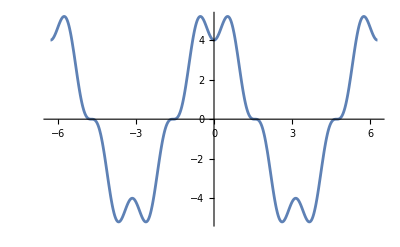

```mathematica
Plot[5 Cos[x]-Cos[5 x],{x,-2π,2π}]
```

```mathematica
D[(5 Cos[x]-Cos[5 x]), x]
```

-5 Sin[x]+5 Sin[5 x]

```mathematica
Solve[-5 Sin[x]+5 Sin[5 x]==0,x]
```

{{x→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-(5 π)/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[-π/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[(5 π)/6+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

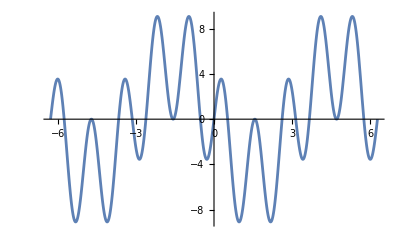

```mathematica
Plot[-5 Sin[x]+5 Sin[5 x],{x,-2π,2π}]
```

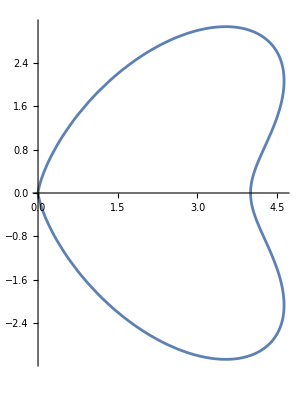

```mathematica
PolarPlot[f[t],{t,0,Pi}]
```